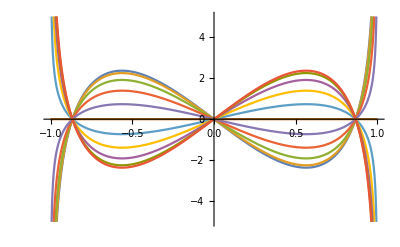

```mathematica
ρ=2Cos[l ArcCos[x/r0]]r0 Cos[α]/Sqrt[r0^2-x^2];
tableplot=Table[ρ/.{l->3,r0->1},{α,0,π,π/10}];
Plot[tableplot,{x,-1,1},PlotRange->{-5,5}]
```

```mathematica
-----------нестационарные----------
```

```mathematica
Integrate[1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)]H0,{xs,-d,d}]
```

1/2 H0 (-Erf[(-d+x)/(2 √t)]+Erf[(d+x)/(2 √t)])

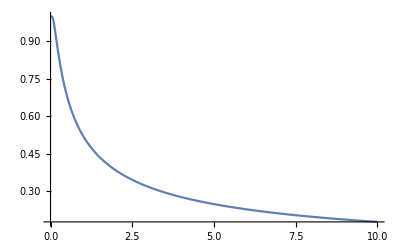

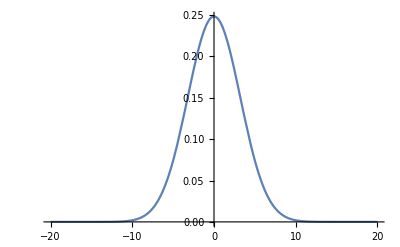

```mathematica
Plot[(1/2 H0 (-Erf[(-d+x)/(2 √t)]+Erf[(d+x)/(2 √t)]))/.{H0->1,d->1,x->0},{t,0.0001,10},PlotRange->All]
Plot[(1/2 H0 (-Erf[(-d+x)/(2 √t)]+Erf[(d+x)/(2 √t)]))/.{H0->1,d->1,t->5},{x,-20,20},PlotRange->All]
```

```mathematica
Integrate[1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)]H0,{xs,-∞,-d}]+Integrate[1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)]H0,{xs,d,∞}]
```

ConditionalExpression[1/2 H0 Erfc[(d-x)/(2 √t)]+1/2 H0 Erfc[(d+x)/(2 √t)],(Re[t]≥0&&Re[x/t]<0)||Re[t]>0]

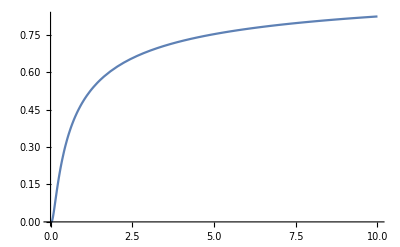

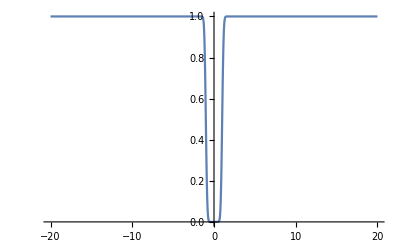

```mathematica
Plot[(1/2 H0 Erfc[(d-x)/(2 √t)]+1/2 H0 Erfc[(d+x)/(2 √t)])/.{H0->1,x->.2,d->1},{t,0.0001,10},PlotRange->All]
Plot[(1/2 H0 Erfc[(d-x)/(2 √t)]+1/2 H0 Erfc[(d+x)/(2 √t)])/.{H0->1,t->.01,d->1},{x,-20,20},PlotRange->All]
```

```mathematica
Integrate[1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)]H0,{xs,0,∞}]
```

ConditionalExpression[1/2 H0 (1+Erf[x/(2 √t)]),(Re[t]≥0&&Re[x/t]<0)||Re[t]>0]

```mathematica
Integrate[1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)] 1/2 H0 (1+Erf[xs/(2 √t0)]),{xs,-∞,0}]
```

$Aborted

```mathematica
al={1,2};
bl={3,4};
Flatten[{al,bl}]
```

{1,2,3,4}

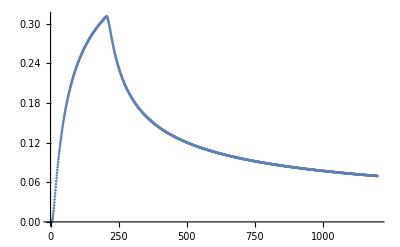

```mathematica
ListPlot[Flatten[{Table[(1/2 H0 (1+Erf[x/(2 √t)]))/.{H0->1,x->-1},{t,0.01,2.01,0.01}],Table[NIntegrate[(1/(Sqrt[4π t])Exp[-(x-xs)^2/(4t)] 1/2 H0 (1+Erf[xs/(2 √t0)]))/.{H0->1,x->-1,t0->2.01},{xs,-∞,0}],{t,0.01,10,0.01}]}]]
```

```mathematica
u=4H0/π Sum[(-1)^k/(2k+1) Exp[-de t (π(2k+1)/(2d))^2]Cos[(2k+1)π x/(2d)],{k,0,100}];
```

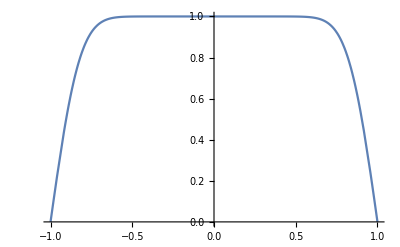

```mathematica
Plot[(u)/.{H0->1,d->1,t->.01,de->1},{x,-1,1},PlotRange->All]
```

```mathematica
u=H0-4H0/π Sum[(-1)^k/(2k+1) Exp[-de t (π(2k+1)/(2d))^2]Cos[(2k+1)π x/(2d)],{k,0,100}];
```

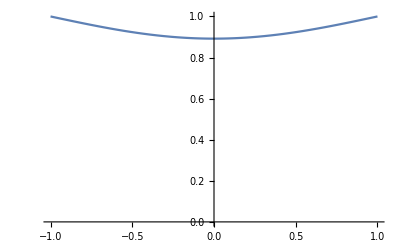

```mathematica
Plot[(u)/.{H0->1,d->1,t->1,de->1},{x,-1,1},PlotRange->{0,1}]
```

```mathematica
i=Integrate[(u Cos[π (2k+1)y/(2d)])/.{H0->1,d->1,t->.01,de->1},{y,-d,d}];
```

```mathematica
u1=H0/d Sum[i Exp[-de t (π(2k+1)/(2d))^2]Cos[(2k+1)π x/(2d)],{k,0,100}];
```

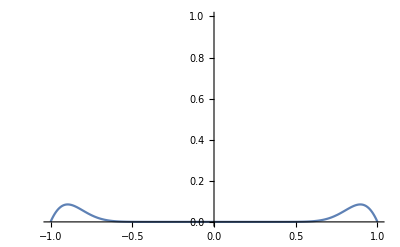

```mathematica
Plot[(u1)/.{H0->1,d->1,t->.1,de->1},{x,-1,1},PlotRange->{0,1}]
```

```mathematica
u=1/(2Sqrt[π de])Integrate[H0 Exp[-x^2/(4de (t-τ))]/(t-τ)^1.5,{τ,0,t}];
```

```mathematica
Plot[u/.{H0->1,t->1,de->1},{x,-10,-.01},PlotRange->{0,1}]
```

$Aborted

```mathematica
u/.{H0->1,t->1,de->1,x->-10}
```

1.53746×10^-13

```mathematica
utable=Table[1/(2Sqrt[π de/.{de->1}])NIntegrate[(H0 Exp[-x^2/(4de (t-τ))]/(t-τ)^(3/2))/.{H0->1,t->1,de->1},{τ,0,(t/.{t->1})-.0001}],{x,-2,0,0.01}];
```

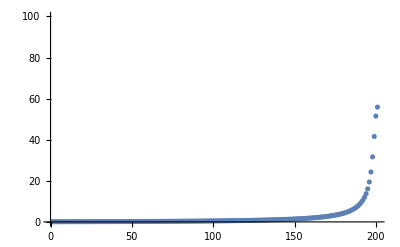

```mathematica
ListPlot[utable,PlotRange->{0,100}]
```

```mathematica
u=H0-1/(2Sqrt[π de t])Integrate[H0 (Exp[-(x-ξ)^2/(4de(t))]-Exp[-(x+ξ)^2/(4de(t))]),{ξ,0,∞}]
```

ConditionalExpression[H0-(√de H0 √t Erf[x/(2 √de √t)])/(√(de t)),Re[1/(de t)]>0]

```mathematica
Integrate[Exp[-(x+ξ)^2/a],{ξ,0,∞}]
```

ConditionalExpression[1/2 √a √π Erfc[x/(√a)],(Re[a]≥0&&Re[x/a]>0)||Re[a]>0]

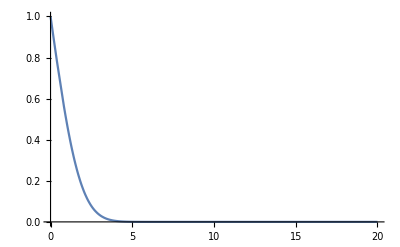

```mathematica
Plot[u/.{H0->1,t->1,de->1},{x,0,20},PlotRange->{0,1}]
```

```mathematica
u1=1/(2Sqrt[π de t])Integrate[H0(1- Erf[ξ/(2 √de √1)])(Exp[-(x-ξ)^2/(4de(t))]-Exp[-(x+ξ)^2/(4de(t))]),{ξ,0,∞}];
```

```mathematica
u1
```

(∫_0^∞ (ⅇ^(-(x-ξ)^2/(4 de t))-ⅇ^(-(x+ξ)^2/(4 de t))) H0 (1-Erf[ξ/(2 √de)])ⅆξ)/(2 √π √(de t))

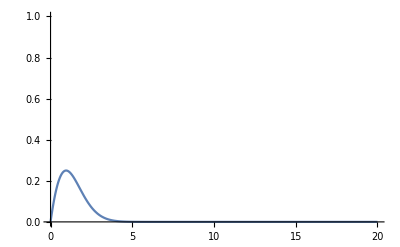

```mathematica
Plot[u1/.{H0->1,t->1,de->1},{x,0,20},PlotRange->{0,1}]
```

```mathematica
Integrate[(a/t1) Exp[-a/t1],{t1,t-t0,t}]
```

ConditionalExpression[a (Gamma[0,a/t]-Gamma[0,a/(t-t0)]),Re[t]≥0&&Re[t]≥Re[t0]&&(Re[t/t0]<0||Re[t/t0]>1||t/t0∉ℝ)]

```mathematica
N[(H0/Sqrt[4π de](2Exp[-x^2/(4 de (t-t0))]/Sqrt[t-t0]-2Exp[-x^2/(4 de (t))]/Sqrt[t]-x^2/(4 de) (-Gamma[0,x^2/(4 de (t))]+Gamma[0,x^2/(4 de (t-t0))])))/.{H0->1,t->2,de->1,t0->1,x->1}]
```

0.128169

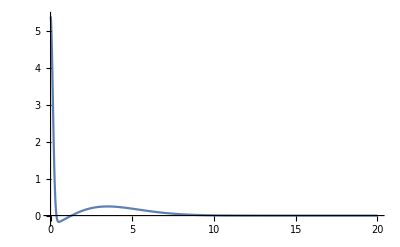

```mathematica
Plot[(H0/Sqrt[4π de](2Exp[-x^2/(4 de (t-t0))]/Sqrt[t-t0]-2Exp[-x^2/(4 de (t))]/Sqrt[t]-x^2/(4 de) (-Gamma[0,x^2/(4 de (t))]+Gamma[0,x^2/(4 de (t-t0))])))/.{H0->1,t->5.01,de->1,t0->5},{x,0,20},PlotRange->All]
```

```mathematica
--------попытки шара в поле-------
```

```mathematica
Hr=(H0 +2m/(r^3))Cos[θ];
Hθ=(H0 +1m/(r^3))Sin[θ];
A=Simplify[Integrate[r Sin[θ]Hr,θ]/Sin[θ]]
A1=Simplify[-Integrate[r Hθ,r]/r]
```

-((2 m+H0 r^3) Cos[θ] Cot[θ])/(2 r^2)

(m/r^2-(H0 r)/2) Sin[θ]

```mathematica
Simplify[-D[-((2 m+H0 r^3) Cos[θ] Cot[θ])/(2 r^2)r,r]/r-Hθ]
```

(-m/r^3+H0 Cos[2 θ]) Csc[θ]

```mathematica
Hr=(H0 +2m/(r^3))Cos[θ];
Hθ=(H0 +1m/(r^3))Sin[θ];
DSolve[{D[A[r,θ] Sin[θ],θ]==r Sin[θ]Hr,-D[r A[r,θ],r]==r Hθ},A[r,θ],{r,θ}]
```

DSolve[{A[r,θ] Cos[θ]+Sin[θ] A^(0,1)[r,θ]==(H0+(2 m)/r^3) r Cos[θ] Sin[θ],-A[r,θ]-r A^(1,0)[r,θ]==(H0+m/r^3) r Sin[θ]},A[r,θ],{r,θ}]

```mathematica
---------попереч поле труба--------
```

```mathematica
Solve[{Hin ==H0+2m/(b^2),-Hin ==-H0+2m/(b^2)+4π/c d σ c3 b,c3==I  w Hin/(c)},{Hin,m,c3}]
```

{{Hin→-(ⅈ c^2 H0)/(-ⅈ c^2+2 b d π w σ),m→-(b^3 d H0 π w σ)/(-ⅈ c^2+2 b d π w σ),c3→(c H0 w)/(-ⅈ c^2+2 b d π w σ)}}

```mathematica
A=Simplify[(((2m/r+H0 r) Sin[ϕ])/.{m->-(b^3 d H0 π w σ)/(-ⅈ c^2+2 b d π w σ)})/.{σ->c^2/(2π w δ^2)}]
```

(H0 (-b^3 d+b d r^2-ⅈ r^2 δ^2) Sin[ϕ])/(r (b d-ⅈ δ^2))

```mathematica
tA=TransformedField["Polar"->"Cartesian",(A),{r,ϕ}->{x,y}]
```

(H0 y (-b^3 d+b d x^2+b d y^2-ⅈ x^2 δ^2-ⅈ y^2 δ^2))/((x^2+y^2) (b d-ⅈ δ^2))

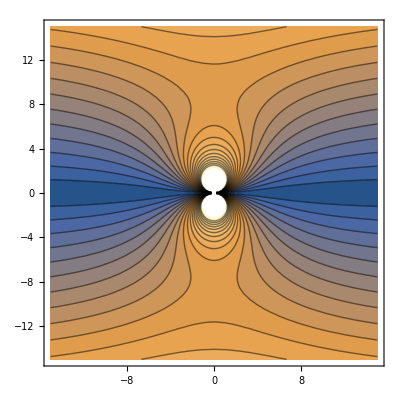

```mathematica
ContourPlot[Abs[tA/.{d->.1,b->10,δ->1,H0->1}],{x,-15,15},{y,-15,15},Contours->20]
```

```mathematica
Hr=Simplify[((Hin Cos[ϕ])/.{Hin->-(ⅈ c^2 H0)/(-ⅈ c^2+2 b d π w σ)})/.{σ->c^2/(2π w δ^2)}];
Hϕ=Simplify[((-Hin Sin[ϕ])/.{Hin->-(ⅈ c^2 H0)/(-ⅈ c^2+2 b d π w σ)})/.{σ->c^2/(2π w δ^2)}];
```

```mathematica
A1=Simplify[Integrate[r Hr,ϕ]]
A2=Simplify[-Integrate[Hϕ,r]]
```

(H0 r δ^2 Sin[ϕ])/(ⅈ b d+δ^2)

(H0 r δ^2 Sin[ϕ])/(ⅈ b d+δ^2)

```mathematica
tA1=TransformedField["Polar"->"Cartesian",(A1),{r,ϕ}->{x,y}]
```

(H0 y δ^2)/(ⅈ b d+δ^2)

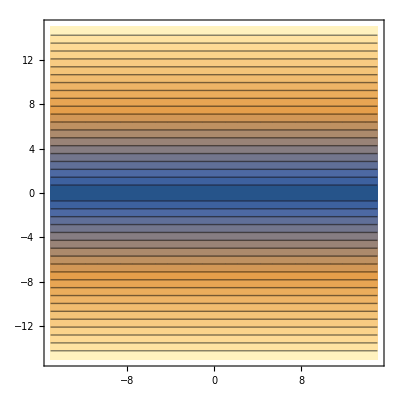

```mathematica
ContourPlot[Abs[tA1/.{d->.1,b->10,δ->1.5,H0->1}],{x,-15,15},{y,-15,15},Contours->20]
```

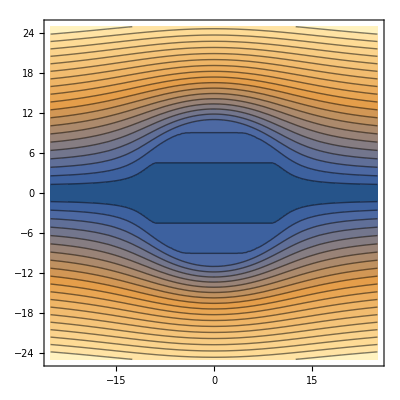

```mathematica
ContourPlot[Abs[tA/.{d->.1,b->10,δ->0.5,H0->1}]HeavisideTheta[-10+Sqrt[x^2+y^2]]+HeavisideTheta[10-Sqrt[x^2+y^2]] Abs[tA1/.{d->.1,b->10,δ->0.5,H0->1}],{x,-25,25},{y,-25,25},Contours->20]
```

```mathematica
----------продольн поле труба----------
```

```mathematica
Solve[{c3 Exp[I k b]+c4 Exp[-I k b]==H0,c3 Exp[I k a]+c4 Exp[-I k a]==c1,c1 p a==k (c3 Exp[I k a]-c4 Exp[-I k a])},{c1,c3,c4}]
```

{{c1→(2 ⅇ^(ⅈ a k+ⅈ b k) H0 k)/(ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ b k) k-a ⅇ^(2 ⅈ a k) p+a ⅇ^(2 ⅈ b k) p),c3→(ⅇ^(ⅈ b k) H0 (k+a p))/(ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ b k) k-a ⅇ^(2 ⅈ a k) p+a ⅇ^(2 ⅈ b k) p),c4→(ⅇ^(2 ⅈ a k+ⅈ b k) H0 (k-a p))/(ⅇ^(2 ⅈ a k) k+ⅇ^(2 ⅈ b k) k-a ⅇ^(2 ⅈ a k) p+a ⅇ^(2 ⅈ b k) p)}}

```mathematica
-----------чао 1 глава------------
```

```mathematica
Er=a(1/(r^(m+1))+(1/(b^(2m)))r^(m-1))Cos[m θ];
Et=a(1/(r^(m+1))-(1/(b^(2m)))r^(m-1))Sin[m θ];
ϕ=a(-1/(m r^m)+(1/(m b^(2m)))r^m)Cos[m θ];
A=ϕ/.{r->θ,θ->-r}
```

a (-θ^-m/m+(b^(-2 m) θ^m)/m) Cos[m r]

(x^2+x^4-y^2+2 x^2 y^2+y^4)/((x^2+y^2)^2)

(2 x y)/((x^2+y^2)^2)

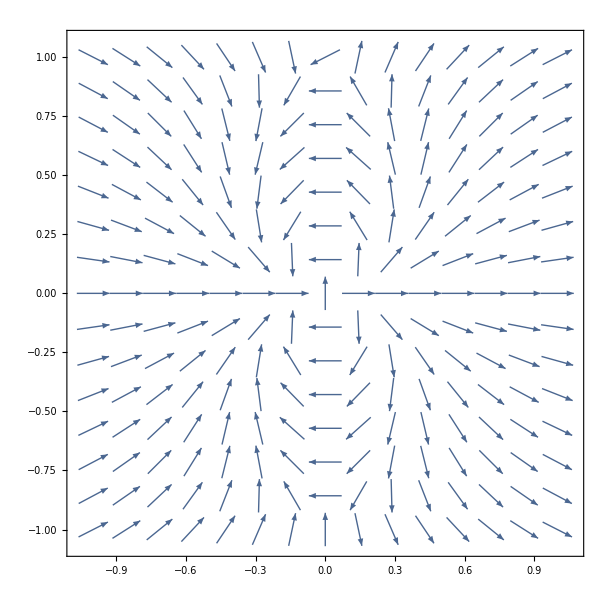

```mathematica
Ex=Simplify[((Er Cos[θ]-Et Sin[θ])/.{θ->ArcTan[x,y],r->Sqrt[x^2+y^2]})/.{m->1,b->1,a->1}]
Ey=Simplify[((Er Sin[θ]+Et Cos[θ])/.{θ->ArcTan[x,y],r->Sqrt[x^2+y^2]})/.{m->1,b->1,a->1}]
VectorPlot[{Ex/Sqrt[Ex^2+Ey^2],Ey/Sqrt[Ex^2+Ey^2]},{x,-1,1},{y,-1,1},VectorScale->{0.05,.2}]
```

```mathematica
ϕ=1/r;
A=ϕ/.{r->θ,θ->-r}
```

1/θ

```mathematica
tf=TransformedField["Polar"->"Cartesian",ϕ,{r,θ}->{x,y}]
tA=TransformedField["Polar"->"Cartesian",1/A,{r,θ}->{x,y}]
```

(a b^(-2 m) (x^2+y^2)^(-m/2) (-b^(2 m)+(x^2+y^2)^m) Cos[m ArcTan[x,y]])/m

(b^(2 m) m (x^2+y^2)^(m/2) Csc[m ArcTan[x,y]])/(a (b^(2 m)+(x^2+y^2)^m))

```mathematica
A=Integrate[r Er,θ]
A1=-Integrate[Et,r]
Simplify[A-A1]
```

(a r^-m (1+b^(-2 m) r^(2 m)) Sin[m θ])/m

-a (-r^-m/m-(b^(-2 m) r^m)/m) Sin[m θ]

0

```mathematica
Ht=a(1/(r^(m+1))+(1/(b^(2m)))r^(m-1))Cos[m θ];
Hr=-a(1/(r^(m+1))-(1/(b^(2m)))r^(m-1))Sin[m θ];
```

```mathematica
Integrate[r Hr,θ]
Simplify[Integrate[Ht,r]]
```

-(a r^-m (-1+b^(-2 m) r^(2 m)) Cos[m θ])/m

-(a (r^-m-b^(-2 m) r^m) Cos[m θ])/m

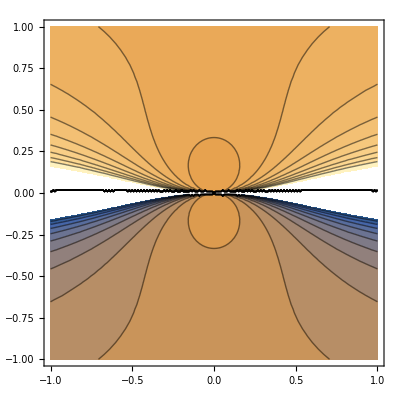

```mathematica
ContourPlot[tA/.{m->1,b->1,a->1},{x,-1,1},{y,-1,1},Contours->20]
```

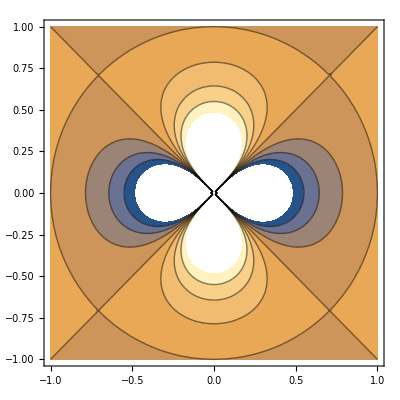

```mathematica
ContourPlot[tf/.{m->2,b->1,a->1},{x,-1,1},{y,-1,1}]
```

```mathematica
----------2 заряда 2мер---------
```

```mathematica
Ex=Q(x+a)/((x+a)^2+(y)^2)-q(x-a)/((x-a)^2+(y)^2)
Ey=Q(y)/((x+a)^2+(y)^2)-q(y)/((x-a)^2+(y)^2)
A=-Integrate[Ex,y]
A1=Integrate[Ey,x]
Simplify[A-A1]
A2=Integrate[Ey,x]-Integrate[Ex,y]
ϕ=Integrate[Ex,x]
ϕ1=Integrate[Ey,y]
Simplify[ϕ-ϕ1]
ϕ2=Integrate[Ex,x]+Integrate[Ey,y]
```

-(q (-a+x))/((-a+x)^2+y^2)+(Q (a+x))/((a+x)^2+y^2)

-(q y)/((-a+x)^2+y^2)+(Q y)/((a+x)^2+y^2)

-q ArcTan[y/(a-x)]-Q ArcTan[y/(a+x)]

q ArcTan[(a-x)/y]+Q ArcTan[(a+x)/y]

-q ArcTan[(a-x)/y]-Q ArcTan[(a+x)/y]-q ArcTan[y/(a-x)]-Q ArcTan[y/(a+x)]

q ArcTan[(a-x)/y]+Q ArcTan[(a+x)/y]-q ArcTan[y/(a-x)]-Q ArcTan[y/(a+x)]

-1/2 q Log[(a-x)^2+y^2]+1/2 Q Log[(a+x)^2+y^2]

-1/2 q Log[a^2-2 a x+x^2+y^2]+1/2 Q Log[a^2+2 a x+x^2+y^2]

0

-1/2 q Log[(a-x)^2+y^2]-1/2 q Log[a^2-2 a x+x^2+y^2]+1/2 Q Log[a^2+2 a x+x^2+y^2]+1/2 Q Log[(a+x)^2+y^2]

```mathematica
A=-q ArcTan[Abs[y],a-x]-Q ArcTan[Abs[y],a+x];
A1=q ArcTan[a-x,Abs[y]]+Q ArcTan[a+x,Abs[y]];
A2=A+A1;
```

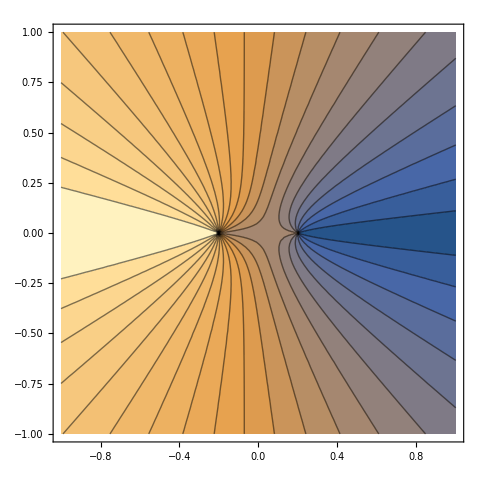

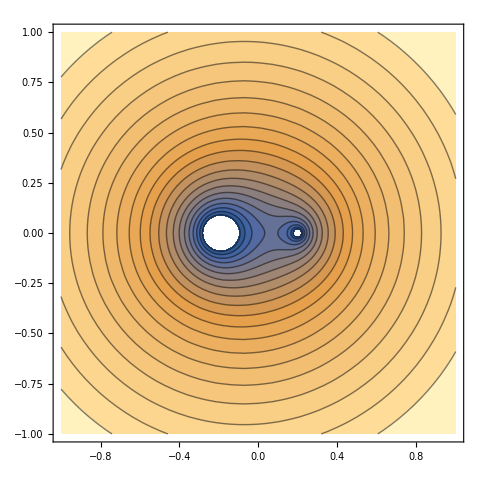

```mathematica
aplot=ContourPlot[(A2+.085)/.{a->.2,Q->1,q->-.5},{x,-1,1},{y,-1,1},Contours->20]
ϕplot=ContourPlot[(ϕ2+.085)/.{a->.2,Q->1,q->-.5},{x,-1,1},{y,-1,1},Contours->20]
```

```mathematica
----------2 заряда 3мер----------
```

```mathematica
Ex=Q(x+a)/((x+a)^2+(y)^2+z^2)^(3/2)-q(x-a)/((x-a)^2+(y)^2+z^2)^(3/2);
Ey=Q(y)/((x+a)^2+(y)^2+z^2)^(3/2)-q(y)/((x-a)^2+(y)^2+z^2)^(3/2);
Ez=Q(z)/((x+a)^2+(y)^2+z^2)^(3/2)-q(z)/((x-a)^2+(y)^2+z^2)^(3/2);
Er=(Cos[ϕ]Sin[θ]Ex+Sin[ϕ]Sin[θ]Ey+Cos[θ]Ez)/.{x->r Cos[ϕ]Sin[θ],y->r Sin[ϕ]Sin[θ],z->r Cos[θ]};
A=r Integrate[Er Sin[θ],θ]/Sin[θ]
```

r Csc[θ] (((a^4 q Cos[θ]-q r^4 Cos[θ]) √(a^2+r^2-a r Sin[θ-ϕ]-a r Sin[θ+ϕ]))/(r (a^4+r^4-2 a^2 r^2 Cos[2 ϕ]) (-a^2-r^2+a r Sin[θ-ϕ]+a r Sin[θ+ϕ]))+1/1+1+(((a^3 q Cos[ϕ])/((a^4+r^4-2 a^2 r^2 Cos[2 ϕ]) √(a^2+r^2-a r Sin[θ-ϕ]-a r Sin[θ+ϕ]))-(a q r^2 Cos[ϕ])/((a^4+r^4-1) √1)-1/1+1/1+(a^2 q r Sin[θ+2 ϕ])/(2 (a^4+r^4-2 a^2 r^2 Cos[2 ϕ]) √(a^2+r^2-a r Sin[θ-ϕ]-a r Sin[θ+ϕ]))) 1)/(((-a^2+r^2 Cos[2 ϕ]) Sec[θ/2]^2 Sec[ϕ] √((a^2+4+r^2 1^2)/(1+1^2)))/(4 r)+4+1/1+(Sec[ϕ] √(1/(1+1)) 1 (1))/(2 r (a^2+r^2-1+(a^2+r^2) (Tan11])^2))))
 |  |  |  |

```mathematica
((((r A Sin[θ])/.{r->Sqrt[x^2+y^2+z^2],θ->ArcCos[z/Sqrt[x^2+y^2+z^2]],ϕ->ArcTan[y/x]})+.085)/.{a->0,Q->1,q->-.5,z->0})/.{x->.1,y->.1}
```

0.085

```mathematica
aplot=ContourPlot[(((r A Sin[θ])/.{r->Sqrt[x^2+y^2+z^2],θ->ArcCos[z/Sqrt[x^2+y^2+z^2]],ϕ->ArcTan[y/x]})+.085)/.{a->0,Q->1,q->-.5,z->0},{x,-1,1},{y,-1,1},Contours->20]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-